```mathematica
e=0.000005;
```

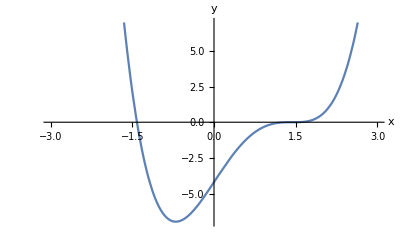

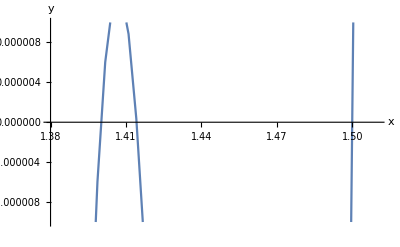

```mathematica
(*1.Определить Subscript[х, 0] графически.*)
Plot[x^4-2.9*x^3+0.1*x^2+5.8*x-4.2,{x,-5,5},AxesLabel->{x,y},PlotRange->{{-3,3},{-7,7}}]
Plot[x^4-2.9*x^3+0.1*x^2+5.8*x-4.2,{x,-5,5},AxesLabel->{x,y},PlotRange->{{1.38,1.51},{-0.00001,0.00001}}]
(*корни уравнения находятся на отрезках: [-2,-1], [1,2], [1.41,1.42], [1.45,2]. Subscript[х, 0]: -2, 1, 1.41, 2*)
```

```mathematica
findRoots[epsi_,x0_]:=Block[{difference=epsi,i=0,root=x0,tmpRoot},
While[difference≥epsi,
tmpRoot=root;
root=root-(root^4-2.9*root^3+0.1*root^2+5.8*root-4.2)/(4*root^3-8.7*root^2+0.2*root+5.8);
difference=tmpRoot-root;
If[difference<0,difference=-difference];
Print["iteration: ",i,"  root: ",root,"  accuracy: ",difference];
i+=1;
];
Return[root];
];
```

```mathematica
(*2. Проверка условий теоремы Конторовича (пункты 1-4).*)
(*1)*) 
ff[x_]=D[x^4-2.9*x^3+0.1*x^2+5.8*x-4.2,x];
{ff[1.39]≠0,ff[1.415]≠0,ff[1.51]≠0,ff[-1.51]≠0}
{B11=Abs[1/ff[1.39]],B12=Abs[1/ff[1.415]],B13=Abs[1/ff[1.51]],B14=Abs[1/ff[-1.51]]};
(*2)*)
{η1=Abs[f[1.39]/ff[1.39]],η2=Abs[f[1.415]/ff[1.415]],η3=Abs[f[1.51]/ff[1.51]],η4=Abs[f[-1.51]/ff[-1.51]]}
(*3)*)
fff[x_]=D[x^4-2.9*x^3+0.1*x^2+5.8*x-4.2,{x,2}];
{K1=Abs[fff[1.39]],K2=Abs[fff[1.415]],K3=Abs[fff[1.51]],K4=Abs[fff[-1.51]]}
(*4)*)
{h1=B11*η1*K1,h2=B12*η2*K2,h3=B13*η3*K3,h4=B14*η4*K4}
```

{True,True,True,True}

{0.00666518,0.000753686,0.00834218,0.0872773}

{0.8008,0.3943,1.2872,53.8352}

{0.476305,0.0789528,0.290736,0.167146}

```mathematica
(*3. Нахождение корней уравнения.*)
Subscript[x, 1]=findRoots[e,1]
Subscript[x, 2]=findRoots[e,1.41]
Subscript[x, 3]=findRoots[e,1.51]
Subscript[x, 4]=findRoots[e,-1.51]
```

iteration: 0  root: 1.15385  accuracy: 0.153846

iteration: 1  root: 1.24997  accuracy: 0.0961287

iteration: 2  root: 1.31103  accuracy: 0.0610557

iteration: 3  root: 1.34971  accuracy: 0.0386754

iteration: 4  root: 1.3737  accuracy: 0.0239941

iteration: 5  root: 1.38793  accuracy: 0.0142319

iteration: 6  root: 1.39566  accuracy: 0.00772329

iteration: 7  root: 1.39906  accuracy: 0.00340983

iteration: 8  root: 1.39994  accuracy: 0.000873306

iteration: 9  root: 1.4  accuracy: 0.0000614004

iteration: 10  root: 1.4  accuracy: 3.01902×10^-7

1.4

iteration: 0  root: 1.41675  accuracy: 0.00675284

iteration: 1  root: 1.41449  accuracy: 0.00226324

iteration: 2  root: 1.41422  accuracy: 0.000271714

iteration: 3  root: 1.41421  accuracy: 4.32468×10^-6

1.41421

iteration: 0  root: 1.50166  accuracy: 0.00834218

iteration: 1  root: 1.50006  accuracy: 0.00160047

iteration: 2  root: 1.5  accuracy: 0.0000572806

iteration: 3  root: 1.5  accuracy: 7.223×10^-8

1.5

iteration: 0  root: -1.42272  accuracy: 0.0872773

iteration: 1  root: -1.41429  accuracy: 0.00843386

iteration: 2  root: -1.41421  accuracy: 0.0000752687

iteration: 3  root: -1.41421  accuracy: 5.9605×10^-9

-1.41421

```mathematica
(*4. Подстановка найденных корней уравнения в исходное уравнение.*)
f[x_]:=x^4-2.9*x^3+0.1*x^2+5.8*x-4.2;
Print["Корни уравнения с точностью до ϵ=1/2*10^-5: x_1 = ",Subscript[x, 1],"; x_2 = ",Subscript[x, 2],"; x_3 = ",Subscript[x, 3],"; x_4 = ",Subscript[x, 4],";"];
{f[Subscript[x, 1]],f[Subscript[x, 2]],f[Subscript[x, 3]],f[Subscript[x, 4]]}
{Round[f[Subscript[x, 1]],e]==0,Round[f[Subscript[x, 2]],e]==0,Round[f[Subscript[x, 3]],e]==0,Round[f[Subscript[x, 4]],e]==0}
```

Корни уравнения с точностью до ϵ=1/2*10^-5: x_1 = 1.4; x_2 = 1.41421; x_3 = 1.5; x_4 = -1.41421;

{-2.75335×10^-14,-3.80851×10^-12,4.44089×10^-15,1.77636×10^-15}

{True,True,True,True}